# BTC-USD Drawdowns

```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
(* Function shortcuts *)
st=StringTemplate;
dollar[a_]:=st["$``"][NumberForm[a,DigitBlock->3]];
(* Default properties for generated plots *)
imagesize=1000;
imagemargins=20;
plotmarkers={None,{"OpenMarkers",8},{"OpenMarkers",8}};
plotstyle={Automatic,Darker[Green],Lighter[Red]};
gridlines={Automatic, Range[0,10^6,5000]};
labelstyle=Directive[14];
titlestyle={20,Red};
subtitlestyle = {15};
plotbackground=Lighter[LightGray,0.75];
updatedstr=Style[st["(updated: ``)"][DateString[]],subtitlestyle];
maniprange=Join[{1,2,3, 6, 9},Range[12,144,6]]//Reverse;
(*origindate="Sep. 14, 2011";*)
origindate="Mar. 28, 2015";
origindate={2011};
btcusd =FinancialData["BTC/USD",origindate];
nbtcusd=btcusd//Normal;
currentprice=Last[Last[nbtcusd]];
```

```mathematica
sigma=0;
peaks=FindPeaks[TimeSeriesResample[btcusd],sigma];
TimeSeriesSelect=ResourceFunction["TimeSeriesSelect"];
newpeaks=Block[{i=-∞},TimeSeriesSelect[peaks,(#2>i&&(i=#2)==i&)]];
```

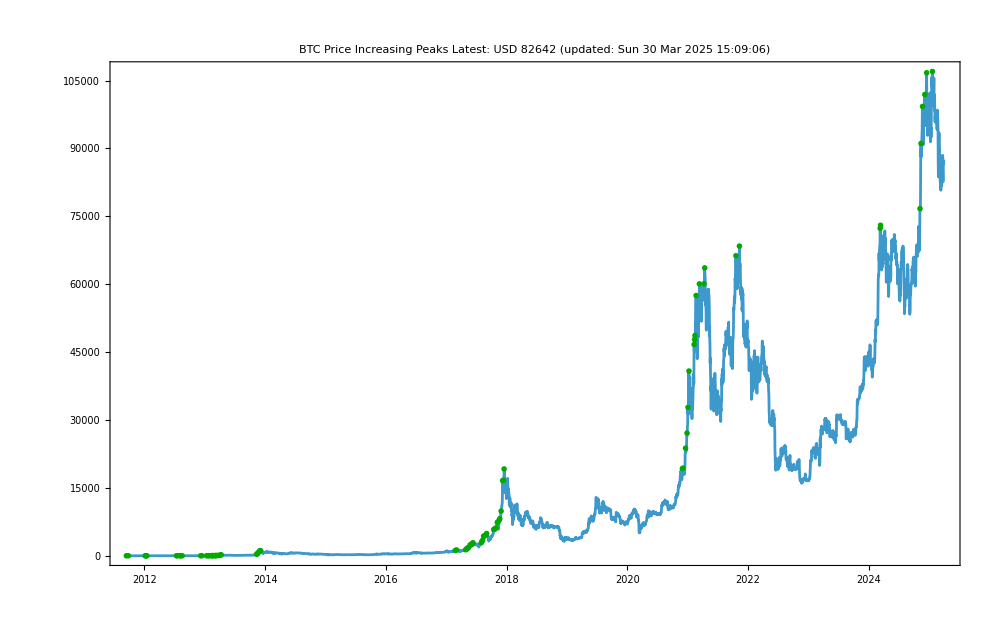

```mathematica
DateListPlot[
{btcusd,newpeaks}
,Joined->{True,False}
,PlotMarkers->plotmarkers
,PlotStyle->plotstyle
,ImageSize->imagesize
,GridLines->gridlines
,PlotLabel->Column[
{
Style[
"BTC Price Increasing Peaks"
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```

```mathematica
newpeakspairs=Partition[newpeaks//Normal,2,1];
newpeakspairs=Join[newpeakspairs,{{Last[Last[newpeakspairs]],btcusd//Normal//Last}}];
```

```mathematica
dd=Join[
# 
,
low=TimeSeriesWindow[btcusd,{First[First[#]],First[Last[#]]}]//Min;
Cases[
Normal[
TimeSeriesWindow[
btcusd,{First[First[#]],First[Last[#]]}
]
]
,{_,low}
]
]&/@newpeakspairs;
```

```mathematica
ddpct={First[#],Last[#],PercentForm[1-(Last[Last[#]]/Last[First[#]])]}&/@dd;
```

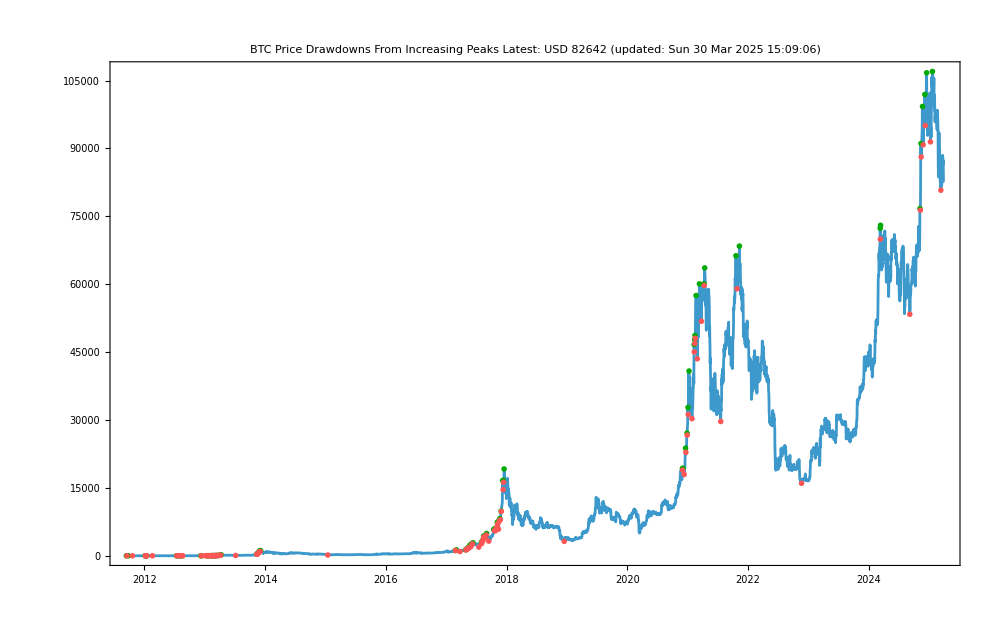

```mathematica
DateListPlot[
{btcusd,First/@ ddpct, #[[2]]&/@ ddpct}
,Joined->{True,False, False}
,PlotMarkers->plotmarkers
,PlotStyle->plotstyle
,ImageSize->imagesize
,GridLines->gridlines
,PlotLabel->Column[
{
Style[
"BTC Price Drawdowns From Increasing Peaks"
,titlestyle
]
,Style[
"Latest: USD " <> ToString[btcusd["LastValue"]//Round]
,subtitlestyle
]
,updatedstr
}
,Center
]
]
```

### Biggest drawdown from high peaks

```mathematica
Grid[
Join[
{{"High","Low","Pct"}}
,ReverseSortBy[ddpct,Last]
]
,Frame->All
]
```

High | Low | Pct
{Thu 5 Dec 2013 00:00:00GMT-4,1132.01} | {Thu 15 Jan 2015 00:00:00GMT-4,171.305} | 84.87%
{Sun 17 Dec 2017 00:00:00GMT-4,19183.4} | {Sun 16 Dec 2018 00:00:00GMT-4,3185.13} | 83.4%
{Wed 10 Nov 2021 00:00:00GMT-4,68420.7} | {Mon 21 Nov 2022 00:00:00GMT-4,16014.5} | 76.59%
{Wed 10 Apr 2013 00:00:00GMT-4,229.} | {Sun 7 Jul 2013 00:00:00GMT-4,66.34} | 71.03%
{Mon 26 Sep 2011 00:00:00GMT-4,6.05} | {Fri 21 Oct 2011 00:00:00GMT-4,2.24} | 62.98%
{Wed 14 Apr 2021 00:00:00GMT-4,63611.3} | {Tue 20 Jul 2021 00:00:00GMT-4,29669.2} | 53.36%
{Mon 16 Jan 2012 00:00:00GMT-4,7.15} | {Sun 19 Feb 2012 00:00:00GMT-4,4.23} | 40.84%
{Fri 17 Aug 2012 00:00:00GMT-4,13.42} | {Mon 20 Aug 2012 00:00:00GMT-4,8.06} | 39.94%
{Sat 2 Sep 2017 00:00:00GMT-4,4921.83} | {Fri 15 Sep 2017 00:00:00GMT-4,3236.96} | 34.23%
{Mon 12 Jun 2017 00:00:00GMT-4,2863.5} | {Mon 17 Jul 2017 00:00:00GMT-4,1918.68} | 33%
{Sat 4 Mar 2017 00:00:00GMT-4,1287.26} | {Sat 25 Mar 2017 00:00:00GMT-4,933.915} | 27.45%
{Wed 13 Mar 2024 00:00:00GMT-4,73025.9} | {Fri 6 Sep 2024 00:00:00GMT-4,53358.9} | 26.93%
{Sat 9 Jan 2021 00:00:00GMT-4,40812.4} | {Wed 27 Jan 2021 00:00:00GMT-4,30293.9} | 25.77%
{Tue 21 Jan 2025 00:00:00GMT-4,107000.} | {Thu 13 Mar 2025 00:00:00GMT-4,80762.1} | 24.52%
{Sun 21 Feb 2021 00:00:00GMT-4,57502.} | {Sun 28 Feb 2021 00:00:00GMT-4,43527.1} | 24.3%
{Thu 9 Nov 2017 00:00:00GMT-4,7460.98} | {Mon 13 Nov 2017 00:00:00GMT-4,5887.96} | 21.08%
{Tue 19 Nov 2013 00:00:00GMT-4,669.01} | {Wed 20 Nov 2013 00:00:00GMT-4,536.01} | 19.88%
{Thu 25 May 2017 00:00:00GMT-4,2403.37} | {Sun 28 May 2017 00:00:00GMT-4,1946.58} | 19.01%
{Wed 14 Sep 2011 00:00:00GMT-4,5.97} | {Sat 17 Sep 2011 00:00:00GMT-4,4.85} | 18.76%
{Sat 30 Nov 2013 00:00:00GMT-4,1131.99} | {Mon 2 Dec 2013 00:00:00GMT-4,955.} | 15.64%
{Tue 17 Dec 2024 00:00:00GMT-4,106717.} | {Thu 9 Jan 2025 00:00:00GMT-4,91451.6} | 14.3%
{Sat 13 Mar 2021 00:00:00GMT-4,60073.8} | {Thu 25 Mar 2021 00:00:00GMT-4,51808.7} | 13.76%
{Fri 8 Dec 2017 00:00:00GMT-4,16615.5} | {Mon 11 Dec 2017 00:00:00GMT-4,14618.3} | 12.02%
{Wed 11 Jan 2012 00:00:00GMT-4,7.14} | {Sun 15 Jan 2012 00:00:00GMT-4,6.3} | 11.76%
{Fri 22 Mar 2013 00:00:00GMT-4,72.23} | {Sun 24 Mar 2013 00:00:00GMT-4,63.9} | 11.53%
{Wed 20 Oct 2021 00:00:00GMT-4,66290.3} | {Wed 27 Oct 2021 00:00:00GMT-4,58997.2} | 11%
{Mon 9 Jan 2012 00:00:00GMT-4,7.} | {Tue 10 Jan 2012 00:00:00GMT-4,6.3} | 10%
{Fri 6 Jan 2012 00:00:00GMT-4,6.65} | {Sat 7 Jan 2012 00:00:00GMT-4,6.} | 9.774%
{Thu 17 Aug 2017 00:00:00GMT-4,4367.75} | {Tue 22 Aug 2017 00:00:00GMT-4,3990.38} | 8.64%
{Fri 22 Nov 2024 00:00:00GMT-4,99273.3} | {Tue 26 Nov 2024 00:00:00GMT-4,90803.2} | 8.532%
{Sun 22 Oct 2017 00:00:00GMT-4,6007.97} | {Wed 25 Oct 2017 00:00:00GMT-4,5517.94} | 8.156%
{Thu 3 Dec 2020 00:00:00GMT-4,19360.9} | {Fri 11 Dec 2020 00:00:00GMT-4,17967.9} | 7.195%
{Tue 12 Mar 2013 00:00:00GMT-4,48.25} | {Wed 13 Mar 2013 00:00:00GMT-4,44.84} | 7.067%
{Fri 6 Dec 2024 00:00:00GMT-4,101916.} | {Mon 9 Dec 2024 00:00:00GMT-4,95042.9} | 6.744%
{Fri 5 May 2017 00:00:00GMT-4,1538.46} | {Sat 6 May 2017 00:00:00GMT-4,1435.07} | 6.72%
{Mon 15 May 2017 00:00:00GMT-4,1781.21} | {Tue 16 May 2017 00:00:00GMT-4,1665.46} | 6.498%
{Thu 19 Jul 2012 00:00:00GMT-4,9.} | {Mon 23 Jul 2012 00:00:00GMT-4,8.42} | 6.444%
{Tue 1 Aug 2017 00:00:00GMT-4,2872.68} | {Thu 3 Aug 2017 00:00:00GMT-4,2702.09} | 5.938%
{Mon 6 Nov 2017 00:00:00GMT-4,7378.92} | {Tue 7 Nov 2017 00:00:00GMT-4,6960.73} | 5.667%
{Fri 12 May 2017 00:00:00GMT-4,1777.} | {Sat 13 May 2017 00:00:00GMT-4,1678.74} | 5.53%
{Sun 10 Nov 2013 00:00:00GMT-4,341.24} | {Mon 11 Nov 2013 00:00:00GMT-4,323.} | 5.345%
{Sun 3 Jan 2021 00:00:00GMT-4,32780.3} | {Mon 4 Jan 2021 00:00:00GMT-4,31211.5} | 4.786%
{Wed 3 May 2017 00:00:00GMT-4,1447.65} | {Thu 4 May 2017 00:00:00GMT-4,1383.82} | 4.409%
{Wed 7 Jun 2017 00:00:00GMT-4,2757.55} | {Thu 8 Jun 2017 00:00:00GMT-4,2641.} | 4.227%
{Tue 15 Aug 2017 00:00:00GMT-4,4320.27} | {Wed 16 Aug 2017 00:00:00GMT-4,4151.98} | 3.895%
{Sat 19 Dec 2020 00:00:00GMT-4,23778.5} | {Mon 21 Dec 2020 00:00:00GMT-4,22863.2} | 3.849%
{Sun 15 Oct 2017 00:00:00GMT-4,5796.96} | {Thu 19 Oct 2017 00:00:00GMT-4,5575.44} | 3.821%
{Tue 9 Feb 2021 00:00:00GMT-4,46695.2} | {Wed 10 Feb 2021 00:00:00GMT-4,45041.6} | 3.541%
{Sun 24 Nov 2013 00:00:00GMT-4,829.15} | {Mon 25 Nov 2013 00:00:00GMT-4,800.05} | 3.51%
{Mon 11 Mar 2024 00:00:00GMT-4,72362.9} | {Tue 12 Mar 2024 00:00:00GMT-4,69967.5} | 3.31%
{Wed 13 Nov 2024 00:00:00GMT-4,91093.7} | {Thu 14 Nov 2024 00:00:00GMT-4,88115.5} | 3.269%
{Fri 14 Dec 2012 00:00:00GMT-4,13.52} | {Thu 3 Jan 2013 00:00:00GMT-4,13.09} | 3.18%
{Fri 1 Feb 2013 00:00:00GMT-4,20.46} | {Sun 3 Feb 2013 00:00:00GMT-4,19.82} | 3.128%
{Fri 28 Apr 2017 00:00:00GMT-4,1331.18} | {Sun 30 Apr 2017 00:00:00GMT-4,1293.28} | 2.847%
{Sat 23 Feb 2013 00:00:00GMT-4,30.4} | {Sun 24 Feb 2013 00:00:00GMT-4,29.54} | 2.829%
{Tue 21 Nov 2017 00:00:00GMT-4,8213.67} | {Fri 24 Nov 2017 00:00:00GMT-4,7982.48} | 2.815%
{Sat 25 Feb 2017 00:00:00GMT-4,1182.54} | {Sun 26 Feb 2017 00:00:00GMT-4,1150.77} | 2.687%
{Sat 4 Aug 2012 00:00:00GMT-4,10.79} | {Sun 5 Aug 2012 00:00:00GMT-4,10.51} | 2.595%
{Fri 11 Jan 2013 12:00:00GMT-4,14.} | {Mon 14 Jan 2013 00:00:00GMT-4,13.64} | 2.571%
{Wed 13 Dec 2017 00:00:00GMT-4,16662.9} | {Thu 14 Dec 2017 00:00:00GMT-4,16253.} | 2.46%
{Fri 17 Nov 2017 00:00:00GMT-4,7849.64} | {Sat 18 Nov 2017 00:00:00GMT-4,7660.55} | 2.409%
{Sun 17 Feb 2013 00:00:00GMT-4,27.5} | {Tue 19 Feb 2013 00:00:00GMT-4,26.92} | 2.109%
{Wed 9 Aug 2017 00:00:00GMT-4,3410.76} | {Thu 10 Aug 2017 00:00:00GMT-4,3340.74} | 2.053%
{Wed 13 Feb 2013 00:00:00GMT-4,25.47} | {Thu 14 Feb 2013 00:00:00GMT-4,25.} | 1.845%
{Fri 12 Feb 2021 00:00:00GMT-4,47782.1} | {Sat 13 Feb 2021 00:00:00GMT-4,46900.6} | 1.845%
{Mon 30 Nov 2020 00:00:00GMT-4,19254.1} | {Tue 1 Dec 2020 00:00:00GMT-4,18927.6} | 1.696%
{Mon 28 Dec 2020 00:00:00GMT-4,27112.2} | {Tue 29 Dec 2020 00:00:00GMT-4,26655.} | 1.686%
{Sun 10 Mar 2013 00:00:00GMT-4,46.} | {Mon 11 Mar 2013 00:00:00GMT-4,45.29} | 1.543%
{Thu 7 Mar 2013 00:00:00GMT-4,42.32} | {Fri 8 Mar 2013 00:00:00GMT-4,41.68} | 1.512%
{Fri 15 Feb 2013 00:00:00GMT-4,27.4} | {Sat 16 Feb 2013 00:00:00GMT-4,27.} | 1.46%
{Sun 14 Feb 2021 00:00:00GMT-4,48661.9} | {Tue 16 Feb 2021 00:00:00GMT-4,48057.8} | 1.241%
{Sat 19 Jan 2013 00:00:00GMT-4,15.57} | {Sun 20 Jan 2013 00:00:00GMT-4,15.38} | 1.22%
{Thu 24 Jan 2013 00:00:00GMT-4,17.5} | {Fri 25 Jan 2013 00:00:00GMT-4,17.29} | 1.2%
{Fri 7 Dec 2012 00:00:00GMT-4,13.45} | {Mon 10 Dec 2012 00:00:00GMT-4,13.29} | 1.19%
{Fri 15 Nov 2013 00:00:00GMT-4,416.95} | {Sat 16 Nov 2013 00:00:00GMT-4,412.} | 1.187%
{Tue 9 May 2017 00:00:00GMT-4,1632.51} | {Wed 10 May 2017 00:00:00GMT-4,1613.66} | 1.155%
{Sat 2 Mar 2013 00:00:00GMT-4,34.55} | {Sun 3 Mar 2013 00:00:00GMT-4,34.16} | 1.129%
{Sun 6 Aug 2017 00:00:00GMT-4,3255.64} | {Mon 7 Aug 2017 00:00:00GMT-4,3226.61} | 0.8917%
{Thu 28 Mar 2013 00:00:00GMT-4,89.3} | {Fri 29 Mar 2013 00:00:00GMT-4,88.52} | 0.8735%
{Tue 7 Aug 2012 00:00:00GMT-4,10.84} | {Wed 8 Aug 2012 00:00:00GMT-4,10.75} | 0.8303%
{Wed 29 Nov 2017 00:00:00GMT-4,9867.62} | {Thu 30 Nov 2017 00:00:00GMT-4,9803.22} | 0.6526%
{Sat 10 Apr 2021 00:00:00GMT-4,60100.8} | {Sun 11 Apr 2021 00:00:00GMT-4,59717.9} | 0.6371%
{Sat 6 Apr 2013 00:00:00GMT-4,141.8} | {Sun 7 Apr 2013 00:00:00GMT-4,141.} | 0.5642%
{Fri 13 Jul 2012 12:00:00GMT-4,7.59} | {Sun 15 Jul 2012 00:00:00GMT-4,7.55} | 0.527%
{Thu 7 Nov 2024 00:00:00GMT-4,76708.8} | {Sat 9 Nov 2024 00:00:00GMT-4,76356.1} | 0.4598%
{Mon 30 Oct 2017 00:00:00GMT-4,6142.15} | {Tue 31 Oct 2017 00:00:00GMT-4,6115.44} | 0.4349%
{Sun 4 Jun 2017 00:00:00GMT-4,2474.01} | {Mon 5 Jun 2017 00:00:00GMT-4,2464.75} | 0.3743%
{Wed 30 Aug 2017 00:00:00GMT-4,4577.75} | {Thu 31 Aug 2017 00:00:00GMT-4,4570.02} | 0.1689%